```mathematica
(-8*Mpi*π*V0)/((p^2 + q^2 - 2*p*q*x + Mpi^2)^2)
```

```mathematica
V[p_,q_,x_,g_,M_,Mrho_] :=  - (4*g*π*Sin[Sqrt[p^2 + q^2 - 2*p*q*x]/Mrho])/(Sqrt[p^2 + q^2 - 2*p*q*x]*M)
```

```mathematica
V[1.2,2.3,0.3,1.01,0.02,1,0.14,0.7]
```

0.427018

```mathematica
Integrate[1/2*V[p,q,x,g,M,Mrho]*LegendreP[l,x],{x,-1,1} ,Assumptions->{Im[q]==0,Im[p]==0}]
```

Integrate[-(2 g π LegendreP[l,x] Sin[(√(p^2+q^2-2 p q x))/Mrho])/(M √(p^2+q^2-2 p q x)),{x,-1,1},Assumptions→{Im[q]==0,Im[p]==0}]

```mathematica
ConditionalExpression[-(2 g π (Mrho Cos[(√((p-q)^2))/Mrho]-Mrho Cos[(√((p+q)^2))/Mrho]))/(M p q), (p/q+q/p∉Reals||Re[p/q+q/p]<-2||Re[p/q+q/p]>2)&&(((Im[p]+Im[q]) (Re[p]+Re[q])≥0&&Im[q] Re[p]+Im[p] Re[q]≤0)||(Im[q] Re[p]+Im[p] Re[q]≥0&&Im[p]^3 Re[q]+Im[q] Re[p] (Im[q]^2-Re[p]^2+Re[q]^2)≤Im[p] (Im[p] Im[q] Re[p]+Re[q] (Im[q]^2-Re[p]^2+Re[q]^2)))||(Im[p] Re[p]+Im[q] Re[q])/(2 Im[q] Re[p]+2 Im[p] Re[q])≥1/2||(Im[p]^3 Re[q]+Im[q] Re[p] (Im[q]^2-Re[p]^2+Re[q]^2)≥Im[p] (Im[p] Im[q] Re[p]+Re[q] (Im[q]^2-Re[p]^2+Re[q]^2))&&(Im[p]+Im[q]) (Re[p]+Re[q])≤0))]
```

```mathematica
V[k_,g_,M_,Mrho_]:=(-4*g*π*Sin[(k)/Mrho])/(k*M)
```

```mathematica
V[p,1,1.01,0.939,0.77]
```

-(10.0248 Sin[1.2987 p])/p

```mathematica
V[p_,q_,g_,M_,Mrho_] :=-(4 g Mrho π Sin[p/Mrho] Sin[q/Mrho])/(M p q)
```

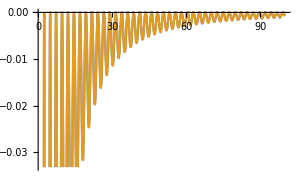

```mathematica
Plot[{V[p,p,1.01,0.939,0.77], -(5.203869236840857 (1. Cos[1.2987012987012987 p-1.2987012987012987 p]-1. Cos[1.2987012987012987 p+1.2987012987012987 p]))/(p p)},{p,0,100}]
```

```mathematica
TrigReduce[-(10.407738473681714 Sin[1.2987012987012987 p] Sin[1.2987012987012987 q])/(p q)]
```

-(5.20387 (1. Cos[1.2987 p-1.2987 q]-1. Cos[1.2987 p+1.2987 q]))/(p q)

```mathematica
V[p,q,1.01,0.939,0.77]
```

-(10.4077 Sin[1.2987 p] Sin[1.2987 q])/(p q)

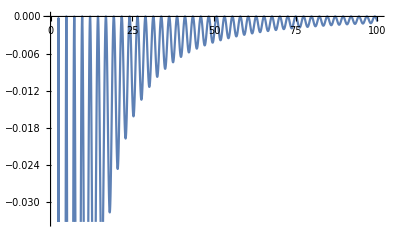

```mathematica
Plot[-(5.203869236840857 (1. Cos[1.2987012987012987 p-1.2987012987012987 p]-1. Cos[1.2987012987012987 p+1.2987012987012987 p]))/(p p),{p,0,100}]
```

```mathematica
CForm[FullSimplify[PadeApproximant[Sin[p/Mrho]/p,{p,0,{50,50}}]]]
```

(32553603161083907410579906876066889527441253249521768579211012186183852439444547221794504255051177541230756303681881905110534591678196438674044\
       30777961297985648592139245574322267792087153097751701645787645344951753531242238830465761454892373783839519440792741209263669957762245059\
       6482068642807724605197098364930129617524616550560340441239453206428222561465303839942905609471155244298991327772672000000000000*
      Power(Mrho,50) - 5312597229762364393292069774427992985232468324012226442951048608071111621216355139862398391650307344053355824888505564516\
       24545586432923563643332400988078516556380876690097542446274066625617894159780986667807054774312877622236996869807672276532015481146800431\
       90413114228926051512172369089859108882493706286642687965451366537585061556080277504533503646081123270514137286152678422260470986445946880\
       00000000000*Power(Mrho,48)*Power(p,2) + 2526429127314960281391037551641502702236114693911300621724461288860538165636424231400392421008647\
       67182135595884897878592598319595950482142745146364056093231366185779607470226749243954201798468161034909515717935320486155377075281849867\
       90456456966787846472988546330797669815321841771710540911945459007130393102624921448424635144759149850786406011489107598968739159075997683\
       9720172558828204300697600000000000*Power(Mrho,46)*Power(p,4) - 
     5549920012364084448752880434968304479347350233147092743270593185002269319280594456262758782864774210488965545045938245126539538746740572763\
       31463874800693652689463810023601380035641876921963937247951603153360845835250105683753700478091960651378704059176931209868135686838120201\
       7708905093300182429749051917702478734682672135124715492869940630014252068879762707618272661149210240543257222184960000000000000*
      Power(Mrho,44)*Power(p,6) + 68889497345011802385969173973220616725419286375235162970354374588927256194471720201244446121693654581084152440\
       32401554963795171573367275809653552712401776880433887610255911498356607448031412130130255080883288117979272748489298148833642012625281749\
       08447569267064024788230390536274430165894689007896753408217776669114558263347417700343558760522629260323736817023077332166832088038144259\
       12934400000000000*Power(Mrho,42)*Power(p,8) - 5412962918219038672757551414776105365967064523297929388949155916164092156364814825791951265\
       52926866610654945888400499901903521867129849040576516054477502708311979042359726926123610149902614707064600646189128533635551458361589722\
       83703452794708772040431738590952470070435043461815980099449194498793138302498558218369407047491444394134420671813245220446866664386648711\
       7486675518028865014333440000000000*Power(Mrho,40)*Power(p,10) + 
     2895284689113328028650143197799472691669365552746232489667914624144097837412040764520598683923033598806050557093331881866182240907747293221\
       53975468261425545892082895124688601084273384429552954404825926642895732791622503768231729426548519599585302349213074034760445081142677784\
       8766131913490426662675009700548379172827881241924818173622316286978269670558696537530941350939421651047483965440000000000*Power(Mrho,38)*
      Power(p,12) - 1108409480791945051526738089674049862635323992227335976833917345880414203602132081033066829279353458077912757646645928618629\
       71678531015666974043649929431965584938255838415599580455254738211001320603639009718611887076977197144271535469563760456212247071573990832\
       54350447998790201502973343984005254638526102182464892335286969046584843771401527839588309968647499734456101960265842271715328000000000*
      Power(Mrho,36)*Power(p,14) + 3149514910888372210304334081089803325993013496018553755663652401098039104314459267571140716026385203342323600\
       83670969921456787413332173274588509513454171114006225938567140100878976498253023065625173687123641309866747011916940154424180471551849319\
       31287006938923561561047428915497813600192928780463745493396527868584984744354762587780952511187050493042920923010475448340236974929477632\
       000000000*Power(Mrho,34)*Power(p,16) - 68253732528847260180559415559546046079542333499680026324390369625407339062313363095735768189998001\
       27236622978301197421368367388572501695403319140246801078570279660795387186399379091363573458008112628830212337069912523569749798379399910\
       02892566969364396856301065970472707363014968831747065442132400071672993786845322602251487596680796975859620271223999623891010513898851580\
       27952128000000000*Power(Mrho,32)*Power(p,18) + 115171818686502430320668326075224012280081425533015751369099509195302639644057636547836487\
       13974695134265527342072008821227388183309375619664340123407824867418838179382489144828896436384881372479532099806383385423199047543090285\
       91305066841728961574380847877798258839261319435961817396684888125850798238734079518006904447146880920555061708557714486426537137822898572\
       00850398399692800000000*Power(Mrho,30)*Power(p,20) - 
     1537479597770723285684933972549232251906463676763759294106741044211098610295358174199433060448815340817154637331408257078762848700188166583\
       27708076444087711617027476682035681495598080853347618771938141208557488809447345537725232169451624207489496626255995255564972816806691565\
       857266232954219413738989482409320490969503241039577164774414938072048522291467462848818876236641075200000000*Power(Mrho,28)*Power(p,22) + 
     1643545076549698034263664157357558107390902945223977623855631054899845672930994719681675222092554651773505398547197846874237723347240918031\
       31556767947615419551678411020982076108376113517414343454303546999361875590669609947439726891784024608216379319734057377411082308404798498\
       982715100333539760419962331563001304867678779318996825823350679536891740334222197034602382562951168000000*Power(Mrho,26)*Power(p,24) - 
     1419622436282771618176876300201344402511088912654636351307542341045205010759396952169219895016699133687386788525486976385975168110777655832\
       03039971370635854203540612934828771398707149802368435113410966477433828220607604396416685255930625417842906418437397959405443577937344365\
       026517135014085773148518209757277091663300569935554093750481458520765993467613463661962849157120000000*Power(Mrho,24)*Power(p,26) + 
     9970263737007359006659533651756564742002128822254597122302314361378345084086821326963349323362039571282476241217450085633362436846880969775\
       53744642001630770808939442089226647298231279276248873454765832193250846948683520855542338949108024733611384335834276950283078200529435668\
       93498610622266876852234117547595166351599052501884336351530701549530885158274288130039218176000000*Power(Mrho,22)*Power(p,28) - 
     5714803650611121620470508306285572084847960443211174539078599635296655368549117611535829175877536128886598178862571473942997839609140575071\
       00139952746182277227351413512192130464649328709305592662370961930359299244961712843336136126420203679035070883057878547474188028427427092\
       53589740005921995192374149795934260527115860238314081963348970979771425444406242160856268800000*Power(Mrho,20)*Power(p,30) + 
     2676525614550056392854282958411410256402836047422507906040943661741034170259786496303997929199159314820980938695308073707812654857888392886\
       83205204173596337936488890027801713669436064675891500403724334578353680574391732352367685391974894462244658641689017475114074291896649254\
       16476764704814323614745769722941428797466993860470429835736046684138990554867099348172800000*Power(Mrho,18)*Power(p,32) - 
     1022690218378029930168550184358369429855617458586245225853940304506480475600429315965556955256166605252661228509928358277249725227025535327\
       12895466619445743386713433938492034360059629959487521229141598088661336681228459817832771284294522864544059693293110445523900545510122559\
       82456131816907502426395150799122028463501489171451012786103400758743524365305476464640000*Power(Mrho,16)*Power(p,34) + 
     3172978519880179424971340005229362493585524146897106574621513445969836554546075472555012476109989750461412319992240662672486679159614132856\
       45839594428298818844510915398089547868377705731935969711291651741796510578973023806846288062310130789038857276159436916042485150273332405\
       7846511089739292066947801885911380827111164689380222200435326872526679709783982080000*Power(Mrho,14)*Power(p,36) - 
     7924210983706676254815539478749594339034630219026159256232783805827704646063579143243485376155728447452945518724704554668746898786877164753\
       24104762372532369360610653862030304378895260709645486873141847636243594052763314354850327275009923184020869641540028252437537438825312096\
       503161884561784274380129928638333079445510961841093676395270922772366659351040000*Power(Mrho,12)*Power(p,38) + 
     1570625702414703621759821319699153916620708985294477394849569283546385244016955985033197587517852032225308753250987191170540377003200915033\
       65307583788180021545491661899134785266548604164132189721968278975984471975506815333692275791663166264087962293584005509979788791258229610\
       714579806631432024778792876647416988518126522886413683810407027082739918720000*Power(Mrho,10)*Power(p,40) - 
     2416584058575594055377317701489157856851146896079646580236864232127766155854989167920186970701380702081214915059340672491031703137418513016\
       17661418261874036719241841393947010183733951931999162113354170578375535199963917447540847184969860854767962741060182595319654514356711435\
       42061597834425897128060830134407268378086126621920051255667718381782048000*Power(Mrho,8)*Power(p,42) + 
     2786573739011394282682070447006331788870260523671086618742859530607442698844915571507209172465844100292530057467539056548880094253927473570\
       94185173902037749449769164102801777878923740127403988440650164028947785026424013902598626836005941711168939612856754322660762474311903301\
       3964088415457297203773580755771373302805171057519319805566401640300800*Power(Mrho,6)*Power(p,44) - 
     2269712388440913858103824920103756010932004590668341070295091390740215659392714661171902365507465992968271433762859161954617216112671408967\
       82767024071652196187060237844967801629012146669614932580007672578769070300202857486439704667754440838609549014013172704048240986289186362\
       067407289059939958500072682194406822341090901746253017054491148000*Power(Mrho,4)*Power(p,46) + 
     1166706108437370991130365310582843360374542474407450409879911557619456381026263838369745348792307751347527239615510226192745066024124106188\
       46823311846146422006324370105424389723575826173857675959086860821247922569199021709752982139975033510042161710639908076958644840683358592\
       43654943409698196493283675643230404258514135949180841420400900*Power(Mrho,2)*Power(p,48) - 
     2852510865991180270912881877282211279246529151052795248676436369979110480299500239332496006355777219572293203811560658097124988110373609176\
       66946374385017829124320856826680014893900505852308967095362938570499416272601157036070876370885216816503629135564929505224315505779699306\
       705912777060284070238165213972045890123111966460163758677*Power(p,50))/
   (663.*(49100457256536813590618260748215519649232659501541129078749641306461315896598110440112374442007809262791487637529233642700655492727294\
         779297201067540894388923809836187716053126211042038508261714956950039899622198394136383692767206055126581806694412057930508917183464101\
         927032353840847765675426432285365155904871990373340296456350438071251060643179822867971800663563960195280777140722460524544000000000000*
        Power(Mrho,51) + 17044237871033711684954455241300442836763280679949972888504789787762260234952649135749469712150162818265996841398906938\
         488231686581725109488294713934848387709981618678981666060871716289439514012810424242961946482567616014431494354602528585870222884002008\
         584661758877883911300736376586594453051661864588395659058580862360331813056983234614139927753517164186564390661988885472646757576658124\
         8000000000000*Power(Mrho,49)*Power(p,2) + 296786178917623624151640379934409496567799089683324365237033760682268166757979266095833093058\
         146183101890191997971166978422341334818601979903657301145099519858406200020775602098330978689268733112035194186234596675365841809267418\
         173641459237221023630291568246022469979982431337017420347863266422405779218484300451771416863016113566573831937679472384782155877188914\
         923799760412554236526592000000000000*Power(Mrho,47)*Power(p,4) + 
       34534581976985977504352442217463191423172847925157056728303630422827715419638271310482042702840452402653939582095151157715389561156413053\
         817642016623169809398340001932332767478113114938577370695401588949850411889603688409509626318513681358261474205549095543347187167344176\
         8567573390388356750482830780856464262368760826473061473916518981560118542325289125262657549664513574256587780915200000000000*
        Power(Mrho,45)*Power(p,6) + 301815444044491941846510943082798072937496280708308542424905228233090890261148160312155643701682197033504534\
         223181654890618003785379767031316246892586813831594183578359507899039579484222925168332286449287624665614789129872054504899269433642975\
         420535186826134885943019864606407957593660639104784147638706302321064578597658418773551905702058395396369151201301841833246132555458858\
         188800000000000*Power(Mrho,43)*Power(p,8) + 2110831418196282534464659565203574858504961660052180736984557244795286617338256644520568261\
         035394440776843074167022998410905620898349102424138695648527541333297561865484683388931353937379764810112109096765369589478135961966528\
         521698648497488633335660327175200072408717561880147321625832891000123168020084189694050579405330266932021058393491934731497049589850165\
         32004008450316042240000000000*Power(Mrho,41)*Power(p,10) + 
       12290457631197852127216847126827806312225096703498587763906793650399563874072579268163639245057673049048989727247506531230683942277579315\
         783217552446973322508964670996713472882774394042917199904452351711058217812827996677040880601215959802158443510552154696832601631496077\
         2092610629977171546303523586484953482805676931786657459686679586656434978726887368107919234356263874723840000000000*Power(Mrho,39)*
        Power(p,12) + 61190675223528351500372892453295933114063316610598611609653230840434111155988062568380619223666608121370169127503894251465\
         412905930557558973270556292603468101171793576725819402446258892630971664144872069455521106266820748969259349044345041415629861672231843\
         048623638815755491672671384495885624843840041859778744194139359349612774077282611182059689298153224334663313103257600000000000*
        Power(Mrho,37)*Power(p,14) + 26547739319344028797283748923872230513317877836138189005503232778591050742277388088445968337737126670956588\
         899565756103231333552057397636236267797112117659118718151583650706246230121686544073736847182772506079117940988575063713973326124448203\
         958879237290607519948871247113372557861180343329624099532445433589584570968089708458001897074221916196473358429299832739042689024000000\
         000*Power(Mrho,35)*Power(p,16) + 101761808584797697666147467674732829239766699862215919141008782098301914978294813575118199110384344842\
         156296131475364159925154602256634938745668051604962161006381769776674222834564954909044838900487402370883902511815349419322341772034914\
         569778967805706075176651556119912467811081048535790461341503702509447714811270603109197746755560870878866032631365768822169911951360000\
         00000*Power(Mrho,33)*Power(p,18) + 3481462529044572103355009550529670228269631496809138700381464595948526303007416424467044665181443995\
         907992328003828533077336866128790154970274831098094420048812493381849494091454865372858180875391949032375607338576484802700195781434602\
         946701430695814456003519138889943791325870679678763224303067293897064936217257971244220799559394109170642108388218540624980213760000000\
         000*Power(Mrho,31)*Power(p,20) + 107093194014276140173093042845649772582121933706650904926745094746594190330735055393397382844436158600\
         288784267866316209120714096653159066175822980653493720858587667660033453638242707866164862413702567753792354377440707621759559255870993\
         5989762171472752019127568427002523041640549026262333264833969963344349210182712069052666648810010503142693435219969913860915200000000*
        Power(Mrho,29)*Power(p,22) + 29772736241051370639262176336518878290091639808627750953871997670931910469335089272448833736172987517935310\
         677348838695875725644739408421540915611693077372532100418911969861695640183300748526649382509148017721711093155370605993275339526171542\
         7236033011385073137357606993388636541842897855404514027434306580076812761068021931348302481349947901776065048399052800000000*
        Power(Mrho,27)*Power(p,24) + 75046143149831436215090578739446481187116752972165314945232671171696488786802626928748964381229730078999488\
         311341017933516205432166070734841637201760761954545688363547259923376978144250960306565993428732959949517330575409896915214953460914457\
         762467989721046375850275210308578396807140830250266383414325910950293522115284283214511339526550807531015321419776000000*Power(Mrho,25)*
        Power(p,26) + 17175563148148106141243336313043904832178836533975683827461907796353036884928863057096605961193964699871663351045674874344\
         240197861943376155685154872144889240997858090306117642985987035347951265099716990931194711686041875109621355778730583534330202421116046\
         626719952515359012509112976934975534346192090909842183083872606166144262709124698886339357048832000000*Power(Mrho,23)*Power(p,28) + 
       35679051436724697540363382796376943162650085331914509030296459609947348481452833178788488660887911539326717929393018792760408714277975271\
         958542038729425977508098370986011019782250680411080048780789190291161903856418622932781813695148657956875173911736440062497310707873168\
         43143433139853388726933321339237453806119457968572747106981875588727430683033600000*Power(Mrho,21)*Power(p,30) + 
       67119920602826837242582514736220407458024866444798623295109292302451309586174904476653593520931606891336592152174289178620579705635227025\
         447448766560643543548118318682282309634031646235410250432817515385855628770281932937063651857499825354920738084531574839681183173050846\
         9770954741534238246695529814213316412406429128190468298254574741802065920000000*Power(Mrho,19)*Power(p,32) + 
       11383686911169516914262107420763816788424521934144422882105560700997386771495187641150985599257527907884323289228754412550516785309068106\
         400174070597161317948002863443282771323343320660054919883024739203366126867330192620434030789696374865301543598703282412695884960322383\
         8852566693551343345991770214116081376561187334451508831727000240878796800000*Power(Mrho,17)*Power(p,34) + 
       17281471006324644332805952531697233224073268862285715283689191778686639576376216839810061189234836023790692714927269841706328382483680486\
         630789478713679636916840158604373466301464344074370389454196020865278191266403083321646014469766524221412509380799639891843189334639377\
         518977561071567965156726955875143216915486974720543258045878710927360000*Power(Mrho,15)*Power(p,36) + 
       23230248772274082665927964116049034128643685943424067140503487154955750915829624834404143559504540864946914493105076279271999781666182936\
         515452189600804973744353232583260715224556429819931273666781087757503767568941723927704911387987064501187320335272324483287903319583098\
         32912904795903085219137009899353038192515516895328651207815749120000*Power(Mrho,13)*Power(p,38) + 
       27214841686386134496353620781802645235811697785492747606851286839989836950972184827770766333437945774756974252809205031534729285236173977\
         181622160989320234169069848744929531069263891081688277780046441217920956107812609479695405103295311857700164660983529978609606193942241\
         1829761795218270179251016163374679217892794047338246569908352000*Power(Mrho,11)*Power(p,40) + 
       27139054341615596232083621399558461842476019335038735427758495618953211606718460217941610299554337149774674549051710601583858686912123962\
         212985099339459774553311461854423534449942113434539865159102703733380463457277607720200241972126302355924165144222433727795621485689740\
         633666133058905092940024838521467909516113962775755340128000*Power(Mrho,9)*Power(p,42) + 
       22214689447063387462487837175695453913643136110835507602150957690351602974851819030289139800870034011448694700208887143367797044728456269\
         848786248020373950387915827500966228498349015153009465523049903578735110994403342357022514417754196471949833240246989906804885454753315\
         03515826752161410560615105093757513645689075540029152000*Power(Mrho,7)*Power(p,44) + 
       14055208156596102778803044982932178678010467135330773044012630441496702825312724108403518866194016821108890042098823925907796039463690913\
         914405356554299283395331849249090530925501714898009709710137477772060663451755065445321222168721785885538988122628334952940328153233599\
         9984618268279150794932211025598355723001764425780000*Power(Mrho,5)*Power(p,46) + 
       61369107812100780107813161465329805720119505877841188511650412051371070855933294962397940043063635291877207799640802858174661774834489097\
         209401745488033384092323434146451675686557617998550794018483577940160741276309813627870051889393244187128959597252535815878332376310662\
         21118999978138190301319478603560351767785582300*Power(Mrho,3)*Power(p,48) + 
       13930460832772605884772189491231174144998803564974140133517580228346533408408365742121934829293740181452242104442641204653969768868113411\
         427286963139158915526178054713537124912730162700465244197081508552351562269840146716512538679952843006710802846030697063723455486214605\
         8384382540586408823020091466789572502036719*Mrho*Power(p,50)))

```mathematica
FullSimplify[(1/Mrho-(109061004303 p^2)/(722459832892 Mrho^3)+(3605886663403 p^4)/(617703157122660 Mrho^5)-(2933434889971 p^6)/(33603051747472704 Mrho^7)+(23704595077729 p^8)/(42339845201815607040 Mrho^9)-(481959816488503 p^10)/(363275871831577908403200 Mrho^11))/(1+(34046903537 p^2)/(2167379498676 Mrho^2)+(1679739379 p^4)/(13726736824948 Mrho^4)+(101555058991 p^6)/(168015258737363520 Mrho^6)+(3924840709 p^8)/(2016183104848362240 Mrho^8)+(37291724011 p^10)/(11008359752472057830400 Mrho^10))]
```

(363275871831577908403200 Mrho^10-54839355237791393068800 Mrho^8 p^2+2120649063015013090560 Mrho^6 p^4-31712777908498486800 Mrho^4 p^6+203385425766914820 Mrho^2 p^8-481959816488503 p^10)/(33 (11008359752472057830400 Mrho^11+172927981842573484800 Mrho^9 p^2+1347091855131859200 Mrho^7 p^4+6653887465090320 Mrho^5 p^6+21429630271140 Mrho^3 p^8+37291724011 Mrho p^10))

```mathematica
Simplify[%52]
```

(363275871831577908403200 Mrho^10-54839355237791393068800 Mrho^8 p^2+2120649063015013090560 Mrho^6 p^4-31712777908498486800 Mrho^4 p^6+203385425766914820 Mrho^2 p^8-481959816488503 p^10)/(33 (11008359752472057830400 Mrho^11+172927981842573484800 Mrho^9 p^2+1347091855131859200 Mrho^7 p^4+6653887465090320 Mrho^5 p^6+21429630271140 Mrho^3 p^8+37291724011 Mrho p^10))

```mathematica
Simplify[%52]
```

(363275871831577908403200 Mrho^10-54839355237791393068800 Mrho^8 p^2+2120649063015013090560 Mrho^6 p^4-31712777908498486800 Mrho^4 p^6+203385425766914820 Mrho^2 p^8-481959816488503 p^10)/(33 (11008359752472057830400 Mrho^11+172927981842573484800 Mrho^9 p^2+1347091855131859200 Mrho^7 p^4+6653887465090320 Mrho^5 p^6+21429630271140 Mrho^3 p^8+37291724011 Mrho p^10))

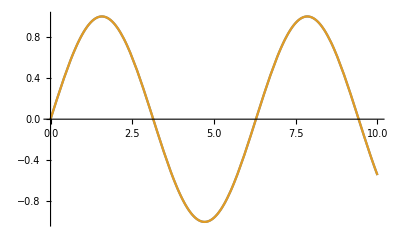

```mathematica
Plot[{Sin[x],(Sin[(√(q^2))/Mrho]+(p √(q^2) (6 Mrho^2 q^2 x Cos[(√(q^2))/Mrho]^3-6 Mrho^2 q^2 x^5 Cos[(√(q^2))/Mrho]^3+4 q^4 x^5 Cos[(√(q^2))/Mrho]^3+3 Mrho^3 √(q^2) x Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+6 Mrho^3 √(q^2) x^3 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-4 Mrho (q^2)^(3/2) x^3 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-9 Mrho^3 √(q^2) x^5 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+4 Mrho (q^2)^(3/2) x^5 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+3 Mrho^2 q^2 x Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2-3 Mrho^2 q^2 x^5 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2+5 q^4 x^5 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2-6 Mrho (q^2)^(3/2) x^3 Sin[(√(q^2))/Mrho]^3+6 Mrho (q^2)^(3/2) x^5 Sin[(√(q^2))/Mrho]^3))/(2 Mrho q^3 (-3 Mrho^2 Cos[(√(q^2))/Mrho]^2+3 Mrho^2 x^4 Cos[(√(q^2))/Mrho]^2-2 q^2 x^4 Cos[(√(q^2))/Mrho]^2-3 q^2 x^4 Sin[(√(q^2))/Mrho]^2))+(p^2 (18 Mrho^3 q^2 Cos[(√(q^2))/Mrho]^3+18 Mrho^3 q^2 x^4 Cos[(√(q^2))/Mrho]^3-12 Mrho q^4 x^4 Cos[(√(q^2))/Mrho]^3-36 Mrho^3 q^2 x^6 Cos[(√(q^2))/Mrho]^3+12 Mrho q^4 x^6 Cos[(√(q^2))/Mrho]^3+9 Mrho^4 √(q^2) Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-27 Mrho^4 √(q^2) x^2 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+18 Mrho^2 (q^2)^(3/2) x^2 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+27 Mrho^4 √(q^2) x^4 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-12 Mrho^2 (q^2)^(3/2) x^4 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-9 Mrho^4 √(q^2) x^6 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-14 q^4 √(q^2) x^6 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]-6 Mrho^2 (q^2)^(3/2) x^6 Cos[(√(q^2))/Mrho]^2 Sin[(√(q^2))/Mrho]+9 Mrho^3 q^2 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2+9 Mrho^3 q^2 x^4 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2-15 Mrho q^4 x^4 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2-18 Mrho^3 q^2 x^6 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2+15 Mrho q^4 x^6 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]^2+27 Mrho^2 (q^2)^(3/2) x^2 Sin[(√(q^2))/Mrho]^3-18 Mrho^2 (q^2)^(3/2) x^4 Sin[(√(q^2))/Mrho]^3-15 q^4 √(q^2) x^6 Sin[(√(q^2))/Mrho]^3-9 Mrho^2 (q^2)^(3/2) x^6 Sin[(√(q^2))/Mrho]^3))/(12 Mrho^2 (q^2)^(3/2) (3 Mrho^2 Cos[(√(q^2))/Mrho]^2-3 Mrho^2 x^4 Cos[(√(q^2))/Mrho]^2+2 q^2 x^4 Cos[(√(q^2))/Mrho]^2+3 q^2 x^4 Sin[(√(q^2))/Mrho]^2)))/(1+(p √(q^2) (3 Mrho^3 √(q^2) x Cos[(√(q^2))/Mrho]^2+6 Mrho^3 √(q^2) x^3 Cos[(√(q^2))/Mrho]^2-4 Mrho (q^2)^(3/2) x^3 Cos[(√(q^2))/Mrho]^2-9 Mrho^3 √(q^2) x^5 Cos[(√(q^2))/Mrho]^2+4 Mrho (q^2)^(3/2) x^5 Cos[(√(q^2))/Mrho]^2+3 Mrho^2 q^2 x Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]-3 Mrho^2 q^2 x^5 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]-q^4 x^5 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]-6 Mrho (q^2)^(3/2) x^3 Sin[(√(q^2))/Mrho]^2+6 Mrho (q^2)^(3/2) x^5 Sin[(√(q^2))/Mrho]^2))/(2 Mrho q^3 (-3 Mrho^2 Cos[(√(q^2))/Mrho]^2+3 Mrho^2 x^4 Cos[(√(q^2))/Mrho]^2-2 q^2 x^4 Cos[(√(q^2))/Mrho]^2-3 q^2 x^4 Sin[(√(q^2))/Mrho]^2))-(p^2 (9 Mrho^4 Cos[(√(q^2))/Mrho]^2-27 Mrho^4 x^2 Cos[(√(q^2))/Mrho]^2+18 Mrho^2 q^2 x^2 Cos[(√(q^2))/Mrho]^2+27 Mrho^4 x^4 Cos[(√(q^2))/Mrho]^2-12 Mrho^2 q^2 x^4 Cos[(√(q^2))/Mrho]^2-9 Mrho^4 x^6 Cos[(√(q^2))/Mrho]^2-6 Mrho^2 q^2 x^6 Cos[(√(q^2))/Mrho]^2+4 q^4 x^6 Cos[(√(q^2))/Mrho]^2+9 Mrho^3 √(q^2) Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]+9 Mrho^3 √(q^2) x^4 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]+3 Mrho (q^2)^(3/2) x^4 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]-18 Mrho^3 √(q^2) x^6 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]-3 Mrho (q^2)^(3/2) x^6 Cos[(√(q^2))/Mrho] Sin[(√(q^2))/Mrho]+27 Mrho^2 q^2 x^2 Sin[(√(q^2))/Mrho]^2-18 Mrho^2 q^2 x^4 Sin[(√(q^2))/Mrho]^2-9 Mrho^2 q^2 x^6 Sin[(√(q^2))/Mrho]^2+3 q^4 x^6 Sin[(√(q^2))/Mrho]^2))/(12 Mrho^2 q^2 (-3 Mrho^2 Cos[(√(q^2))/Mrho]^2+3 Mrho^2 x^4 Cos[(√(q^2))/Mrho]^2-2 q^2 x^4 Cos[(√(q^2))/Mrho]^2-3 q^2 x^4 Sin[(√(q^2))/Mrho]^2)))},{x,0,10}]
```

```mathematica
ExternalEvaluate["Julia","FullSimplify[PadeApproximant[Sin[FractionBox[p, Mrho]]/p,{p,0,{3,3}}]]"]
```

ExternalEvaluate::help: For help configuring the Julia evaluator, see Configure Julia for ExternalEvaluate.

ExternalEvaluate::replFail: The process for external system Julia (C:\Users\risha\AppData\Local\Programs\Julia-1.8.3\bin\julia.exe) failed to start due to: no input returned from process.

$Failed